```mathematica
libraryPath = "PATH TO LIBRARY/libbilliard.dylib"; (* CHANGE THIS *)
billmin=LibraryFunctionLoad[libraryPath,"minimize",{Real, Real, Integer, Real},NumericArray]
zout=LibraryFunctionLoad[libraryPath,"zoutside",{Real, Real},NumericArray]
zin=LibraryFunctionLoad[libraryPath,"zinside",{Real, Real},NumericArray]
```

LibraryFunction[…]

LibraryFunction[…]

LibraryFunction[…]

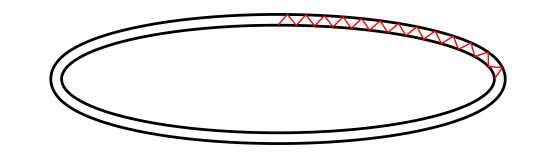

```mathematica
si = 0;
n = 25;
δ = .1;
ParametricPlot[
{
Normal[zin[s, δ]], 
Normal[zout[s, δ]]
},
{s, 0,2Pi} ,
Epilog->
{Red,Line[
Join[ 
Normal[zout[si,δ]],
Normal[billmin[si,Pi/2, n, δ]],
 If[ OddQ[n],Normal[zout[Pi/2, δ]], Normal[zin[Pi/2, δ]]]
]
]
},
PlotStyle->Black,
AxesStyle->Thick,
TicksStyle->Directive[16],
Axes->False,
Ticks->False
]
```